```mathematica
f1n0[n_]:=Sqrt[n]
```

```mathematica
f2n0[n_]:=Sqrt[n/2]
```

```mathematica
f2n1[n_]:=Sqrt[(n-1)/2+1/8]
```

```mathematica
f3n0[n_]:=Sqrt[n/3]
```

```mathematica
f4n0[n_]:=Sqrt[n/4]
```

```mathematica
f5n0[n_]:=Sqrt[n/5]
```

```mathematica
f6n0[n_]:=Sqrt[n/6]
```

```mathematica
Plot[{f1n0[x]^2,f2n0[x]^2,f2n1[x]^2,f3n0[x]^2},{x,1,20,1},AspectRatio->Automatic]
```

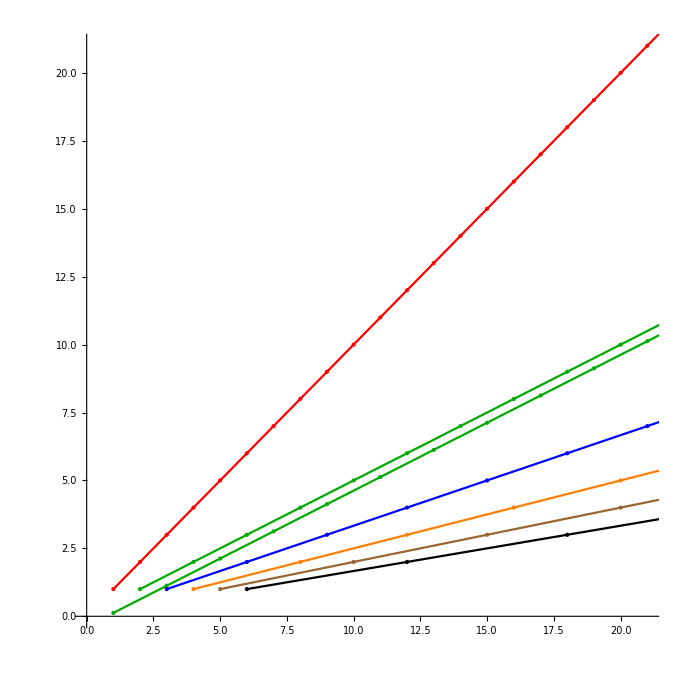

```mathematica
Show[ListPlot[Table[{n,f1n0[n]^2},{n,1,25}],MeshStyle->Directive[PointSize[Large]],Mesh->True,Joined->True,PlotStyle->Red],ListPlot[Table[{n,f2n0[n]^2},{n,2,25,2}],MeshStyle->Directive[PointSize[Large]],Mesh->True,Joined->True,PlotStyle->Darker[Green]],ListPlot[Table[{n,f2n1[n]^2},{n,1,25,2}],MeshStyle->Directive[PointSize[Large]],Mesh->True,Joined->True,PlotStyle->Darker[Green]],ListPlot[Table[{n,f3n0[n]^2},{n,3,25,3}],MeshStyle->Directive[PointSize[Large]],Mesh->True,Joined->True,PlotStyle->Blue],ListPlot[Table[{n,f4n0[n]^2},{n,4,25,4}],MeshStyle->Directive[PointSize[Large]],Mesh->True,Joined->True,PlotStyle->Orange],ListPlot[Table[{n,f5n0[n]^2},{n,5,25,5}],MeshStyle->Directive[PointSize[Large]],Mesh->True,Joined->True,PlotStyle->Brown],ListPlot[Table[{n,f6n0[n]^2},{n,6,25,6}],MeshStyle->Directive[PointSize[Large]],Mesh->True,Joined->True,PlotStyle->Black],PlotRange->{{0,21},{0,21}},AspectRatio->Automatic]
```

```mathematica
list01n00=ReadList["temp01.00",{Number,Number,Number}];
```

```mathematica
list02n00=ReadList["temp02.00",{Number,Number,Number}];
```

```mathematica
list02n01=ReadList["temp02.01",{Number,Number,Number}];
```

```mathematica
list03n00=ReadList["temp03.00",{Number,Number,Number}];
```

```mathematica
list03n01=ReadList["temp03.01",{Number,Number,Number}];
```

```mathematica
list03n02=ReadList["temp03.02",{Number,Number,Number}];
```

```mathematica
list04n00=ReadList["temp04.00",{Number,Number,Number}];
```

```mathematica
list04n01=ReadList["temp04.01",{Number,Number,Number}];
```

```mathematica
list04n02=ReadList["temp04.02",{Number,Number,Number}];
```

```mathematica
list04n03=ReadList["temp04.03",{Number,Number,Number}];
```

```mathematica
list05n00=ReadList["temp05.00",{Number,Number,Number}];list05n01=ReadList["temp05.01",{Number,Number,Number}];list05n02=ReadList["temp05.02",{Number,Number,Number}];list05n03=ReadList["temp05.03",{Number,Number,Number}];list05n04=ReadList["temp05.04",{Number,Number,Number}];
```

```mathematica
list06n00=ReadList["temp06.00",{Number,Number,Number}];list06n01=ReadList["temp06.01",{Number,Number,Number}];list06n02=ReadList["temp06.02",{Number,Number,Number}];list06n03=ReadList["temp06.03",{Number,Number,Number}];list06n04=ReadList["temp06.04",{Number,Number,Number}];
list06n05=ReadList["temp06.05",{Number,Number,Number}];
```

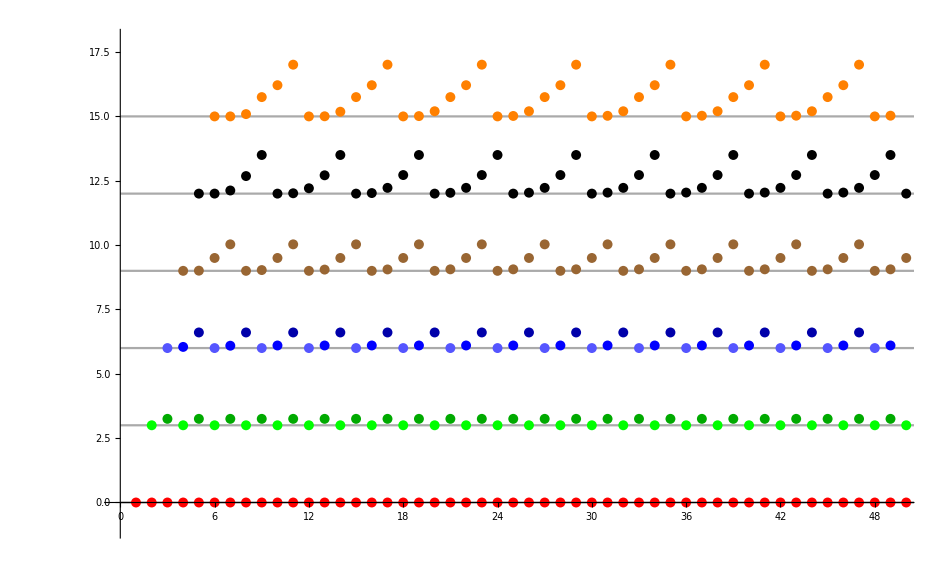

```mathematica
MyOffset=3;MyPS=0.0075;Show[ListPlot[Table[{{0,MyOffset m},{101,MyOffset m}},{m,0,5}],Joined->True,PlotStyle->{Lighter[Gray]}],ListPlot[Transpose[{list01n00[[;;,2]],1list01n00[[;;,3]]^2-(list01n00[[;;,2]]-0)+0 MyOffset}],Mesh->True,PlotStyle->{Red,PointSize[MyPS]}],ListPlot[Transpose[{list02n00[[;;,2]],2list02n00[[;;,3]]^2-(list02n00[[;;,2]]-0)+1 MyOffset}],Mesh->True,PlotStyle->{Green,PointSize[MyPS]}],ListPlot[Transpose[{list02n01[[;;,2]],2list02n01[[;;,3]]^2-(list02n01[[;;,2]]-1)+1 MyOffset}],Mesh->True,PlotStyle->{Darker[Green],PointSize[MyPS]}],ListPlot[Transpose[{list03n00[[;;,2]],3list03n00[[;;,3]]^2-(list03n00[[;;,2]]-0)+2 MyOffset}],Mesh->True,PlotStyle->{Lighter[Blue],PointSize[MyPS]}],ListPlot[Transpose[{list03n01[[;;,2]],3list03n01[[;;,3]]^2-(list03n01[[;;,2]]-1)+2 MyOffset}],Mesh->True,PlotStyle->{Blue,PointSize[MyPS]}],ListPlot[Transpose[{list03n02[[;;,2]],3list03n02[[;;,3]]^2-(list03n02[[;;,2]]-2)+2 MyOffset}],Mesh->True,PlotStyle->{Darker[Blue],PointSize[MyPS]}],ListPlot[Transpose[{list04n00[[;;,2]],4list04n00[[;;,3]]^2-(list04n00[[;;,2]]-0)+3 MyOffset}],Mesh->True,PlotStyle->{Brown,PointSize[MyPS]}],ListPlot[Transpose[{list04n01[[;;,2]],4list04n01[[;;,3]]^2-(list04n01[[;;,2]]-1)+3 MyOffset}],Mesh->True,PlotStyle->{Brown,PointSize[MyPS]}],ListPlot[Transpose[{list04n02[[;;,2]],4list04n02[[;;,3]]^2-(list04n02[[;;,2]]-2)+3 MyOffset}],Mesh->True,PlotStyle->{Brown,PointSize[MyPS]}],ListPlot[Transpose[{list04n03[[;;,2]],4list04n03[[;;,3]]^2-(list04n03[[;;,2]]-3)+3MyOffset}],Mesh->True,PlotStyle->{Brown,PointSize[MyPS]}],ListPlot[Transpose[{list05n00[[;;,2]],5list05n00[[;;,3]]^2-(list05n00[[;;,2]]-0)+4 MyOffset}],Mesh->True,PlotStyle->{Black,PointSize[MyPS]}],ListPlot[Transpose[{list05n01[[;;,2]],5list05n01[[;;,3]]^2-(list05n01[[;;,2]]-1)+4 MyOffset}],Mesh->True,PlotStyle->{Black,PointSize[MyPS]}],ListPlot[Transpose[{list05n02[[;;,2]],5list05n02[[;;,3]]^2-(list05n02[[;;,2]]-2)+4 MyOffset}],Mesh->True,PlotStyle->{Black,PointSize[MyPS]}],ListPlot[Transpose[{list05n03[[;;,2]],5list05n03[[;;,3]]^2-(list05n03[[;;,2]]-3)+4 MyOffset}],Mesh->True,PlotStyle->{Black,PointSize[MyPS]}],ListPlot[Transpose[{list05n04[[;;,2]],5list05n04[[;;,3]]^2-(list05n04[[;;,2]]-4)+4 MyOffset}],Mesh->True,PlotStyle->{Black,PointSize[MyPS]}],ListPlot[Transpose[{list06n00[[;;,2]],6list06n00[[;;,3]]^2-(list06n00[[;;,2]]-0)+5 MyOffset}],Mesh->True,PlotStyle->{Orange,PointSize[MyPS]}],ListPlot[Transpose[{list06n01[[;;,2]],6list06n01[[;;,3]]^2-(list06n01[[;;,2]]-1)+5MyOffset}],Mesh->True,PlotStyle->{Orange,PointSize[MyPS]}],ListPlot[Transpose[{list06n02[[;;,2]],6list06n02[[;;,3]]^2-(list06n02[[;;,2]]-2)+5 MyOffset}],Mesh->True,PlotStyle->{Orange,PointSize[MyPS]}],ListPlot[Transpose[{list06n03[[;;,2]],6list06n03[[;;,3]]^2-(list06n03[[;;,2]]-3)+5 MyOffset}],Mesh->True,PlotStyle->{Orange,PointSize[MyPS]}],ListPlot[Transpose[{list06n04[[;;,2]],6list06n04[[;;,3]]^2-(list06n04[[;;,2]]-4)+5 MyOffset}],Mesh->True,PlotStyle->{Orange,PointSize[MyPS]}],ListPlot[Transpose[{list06n05[[;;,2]],6list06n05[[;;,3]]^2-(list06n05[[;;,2]]-5)+5 MyOffset}],Mesh->True,PlotStyle->{Orange,PointSize[MyPS]}],AxesOrigin->{0,0},PlotRange->{{0,49.5},{-1,18}}]
```

```mathematica
ClearAll[a1,b1,a2,b2,a3,b3]
```

```mathematica
TrigExpand[Sin[a1 t+b1]Sin[a2 t+b2]]
```

Cos[a1 t] Cos[a2 t] Sin[b1] Sin[b2]+Cos[b1] Cos[a2 t] Sin[b2] Sin[a1 t]+Cos[b2] Cos[a1 t] Sin[b1] Sin[a2 t]+Cos[b1] Cos[b2] Sin[a1 t] Sin[a2 t]

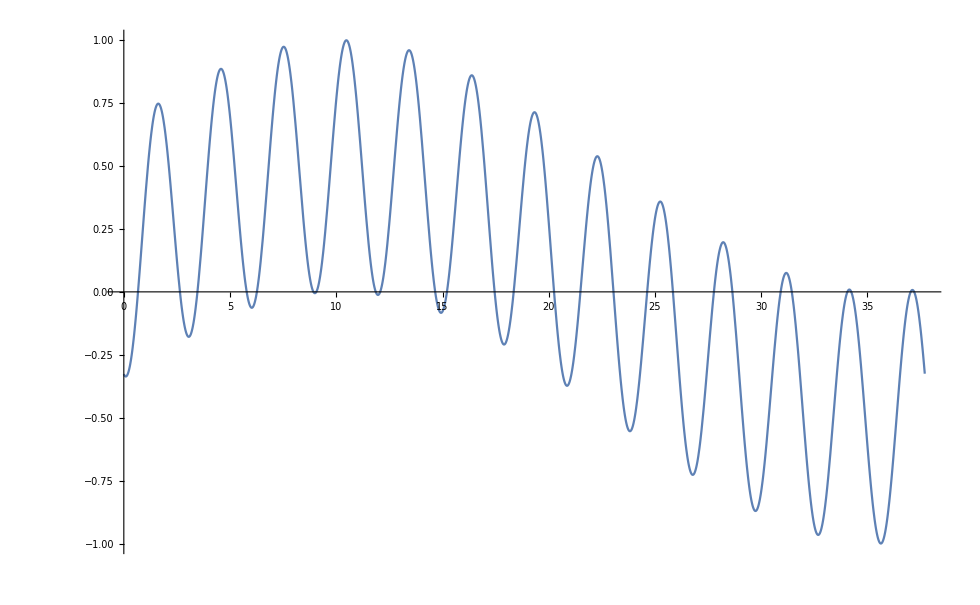

```mathematica
Plot[Sin[1t+0.5]Sin[1.123t-0.75],{t,0,12Pi}]
```

```mathematica
TrigExpand[Sin[1t+0.5]Sin[1.123t-0.75]]
```

(-0.326795+0. ⅈ) Cos[t] Cos[(1.123+0. ⅈ) t]-(0.598194+0. ⅈ) Cos[(1.123+0. ⅈ) t] Sin[t]+(0.35079+0. ⅈ) Cos[t] Sin[(1.123+0. ⅈ) t]+(0.642117+0. ⅈ) Sin[t] Sin[(1.123+0. ⅈ) t]

```mathematica
FullSimplify[(-0.32679502965768803+0. ⅈ) Cos[t] Cos[(1.123+0. ⅈ) t]-(0.5981942893050548+0. ⅈ) Cos[(1.123+0. ⅈ) t] Sin[t]+(0.35079033005053173+0. ⅈ) Cos[t] Sin[(1.123+0. ⅈ) t]+(0.6421173920529568+0. ⅈ) Sin[t] Sin[(1.123+0. ⅈ) t]]
```

0.157661 Cos[0.123 t]-0.484456 Cos[2.123 t]+0.474492 Sin[0.123 t]-0.123702 Sin[2.123 t]